## Poisson-equation approach, Series treatment -- (0, 2Pi) integration, all periodic BC

### set up

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
(*Clear[H0,H0c,H0s,I0cch,I0csh,I0sch,I0ssh,A0c,dA0c]*)
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
pv10[bJx_,bmux_,theta1_,theta2_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]

H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
A1[0,j_,theta1_]:=Integrate[h1[0,j](theta1-t1),{t1,0,theta1}]
A1[n_,j_,theta1_]:=2/n Integrate[h1[n,j]Sinh[n/2(theta1-t1)],{t1,0,theta1}]-2Cosh[n/2 theta1]/(n Sinh[n Pi])Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
dA1[0,j_,theta1_]:=Integrate[h1[0,j],{t1,0,theta1}]
dA1[n_,j_,theta1_]:=Integrate[h1[n,j]Cosh[n/2(theta1-t1)],{t1,0,theta1}]-2Sinh[n/2 theta1]/Sinh[n Pi]Integrate[h1[n,j]Cosh[n/2(2Pi-t1)],{t1,0,2Pi}]
```

```mathematica
Flatten[Table[{n,j,H0[0,j,t1_]:=Release[H0[0,j,t1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0c[n,j,t1_]:=Release[H0c[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,H0s[n,j,t1_]:=Release[H0s[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0cch[n,j,t1_]:=Release[I0cch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0sch[n,j,t1_]:=Release[I0sch[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0csh[n,j,t1_]:=Release[I0csh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,I0ssh[n,j,t1_]:=Release[I0ssh[n,j,t1]]},{n,1,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,A0c[n,j,theta1_]:=Release[A0c[n,j,theta1]]},{n,0,5},{j,0,5}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,dA0c[0,j,theta1_]:=Release[dA0c[0,j,theta1]]},{j,0,10}]//Simplify,1];
```

```mathematica
Flatten[Table[{n,j,h1[n,j]=H1[n,j,t1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

```mathematica
Flatten[Table[{n,j,da0[n,j]=dA0[n,j,theta1]},{n,0,10},{j,0,10}]//Simplify,1]//TableForm;
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

### A0ns and dA0ns

```mathematica
Clear[bJ];
Clear[bmu];
```

```mathematica
Clear[bJ];Clear[bmu];
Clear[Ax0];Clear[dAx0];
```

```mathematica
Ax0[theta1_,bJ_]:=bmu (BesselI[0,bJ]+BesselI[1,bJ]) (-1+Cos[theta1])
dAx0[theta1_,bJ_]:=-bmu (BesselI[0,bJ]+BesselI[1,bJ]) Sin[theta1]
```

```mathematica
Axc0[n_,theta1_,bJ_]:=1/(bJ+4 bJ n^4)2 bmu (((bJ+2 bJ n^2) BesselI[-1+n,bJ]+(bJ-n+2 (1+bJ) n^2-2 n^3) BesselI[n,bJ]) Cos[theta1] Cos[n theta1]+n (2 bJ BesselI[-1+n,bJ]+(1+2 bJ+2 (-1+n) n) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
Axc0[0,theta1_,bJ_]:=Ax0[theta1,bJ]
```

```mathematica
dAxc0[n_,theta1_,bJ_]:=1/(1+4 n^4)bmu (2 BesselI[n,bJ] (-Cos[n theta1] Sin[theta1]+n (1-2 n^2) Cos[theta1] Sin[n theta1])+BesselI[-1+n,bJ] ((1+n) Sin[(-1+n) theta1]+2 n^3 Sin[theta1-n theta1])+(-1+n-2 n^3) BesselI[1+n,bJ] Sin[theta1+n theta1])
dAxc0[0,theta1_,bJ_]:=dAx0[theta1,bJ]
```

```mathematica
Axs0[n_,theta1_,bJ_]:=1/(1+4 n^4)bmu ((1+2 n (1+n)) BesselI[-1+n,bJ] Sin[(-1+n) theta1]+2 BesselI[n,bJ] (-2 n Cos[n theta1] Sin[theta1]+(1+2 n^2) Cos[theta1] Sin[n theta1])+(1+2 (-1+n) n) BesselI[1+n,bJ] Sin[theta1+n theta1])
Axs0[0,theta1_,bJ_]:=0
```

```mathematica
dAxs0[n_,theta1_,bJ_]:=1/(bJ+4 bJ n^4)(-2 bmu n (BesselI[n,bJ]+(-1+2 n^2) (-bJ BesselI[-1+n,bJ]+(-bJ+n) BesselI[n,bJ])) Cos[theta1] Cos[n theta1]-2 bmu (bJ BesselI[-1+n,bJ]+(bJ+n (-1+n-2 n^3)) BesselI[n,bJ]) Sin[theta1] Sin[n theta1])
dAxs0[0,theta1_,bJ_]:=0
```

```mathematica
pvx10[theta1_,theta2_,nmax_]:=Sum[Release[dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2]],{n,0,nmax}]
pvx20[theta1_,theta2_,nmax_]:=Sum[Release[n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2]],{n,1,nmax}]
pvx10n[theta1_,theta2_,n_]:=Release[dAxs0[n,theta1]Sin[n theta2]+dAxc0[n,theta1]Cos[n theta2]]
pvx20n[theta1_,theta2_,n_]:=Release[n Axs0[n,theta1]Cos[n theta2]-n Axc0[n,theta1]Sin[n theta2]]
```

### Plot

#### plots for Ans

```mathematica
bJ=1;
bmu=1;
Qx0=0;
```

A0c tested

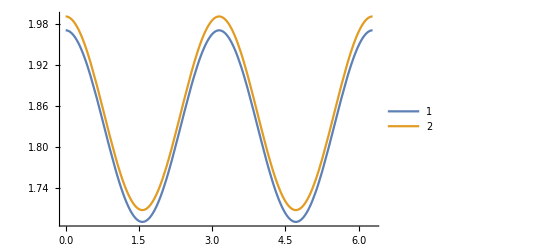

```mathematica
Plot[{Sum[A0c[0,j,theta1],{j,0,5}]*1,Axc0[0,theta1,bJ]*1,Axc0[0,theta1,bJ]*1},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{Sum[A0c[1,j,theta1],{j,0,5}]*1,Axc0[1,theta1,bJ]*1,Axc0[1,theta1,bJ]*1.05},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{Sum[A0c[5,j,theta1],{j,0,5}]*1,Axc0[5,theta1,bJ]*1,Axc0[5,theta1,bJ]*1.05},{theta1,0,2Pi},PlotLegends->Automatic];
Plot[{Sum[A0c[1,j,theta1],{j,0,5}],Axc0[1,theta1,bJ]*1.01},{theta1,0,2Pi},PlotLegends->Automatic]
```

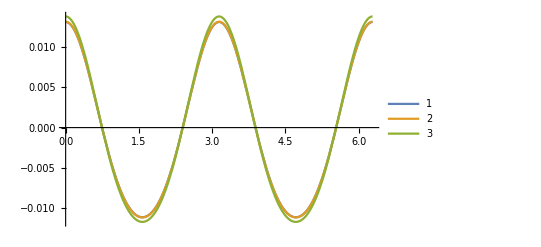

```mathematica
Plot[{Sum[A0c[3,j,theta1],{j,0,5}],Axc0[3,theta1,bJ],Axc0[3,theta1,bJ]*1.05},{theta1,0,2Pi},PlotLegends->Automatic]
```

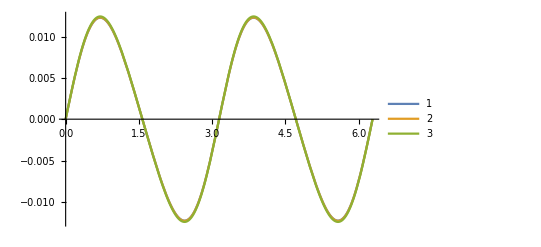

```mathematica
Plot[{Sum[A0s[3,j,theta1],{j,0,5}],Axs0[3,theta1,bJ],Axs0[3,theta1,bJ]*1.01},{theta1,0,2Pi},PlotLegends->Automatic]
```

```mathematica
D[Axs0[n,theta1,bJ],theta1]-dAxs0[n,theta1,bJ]//FullSimplify
```

0

1

1

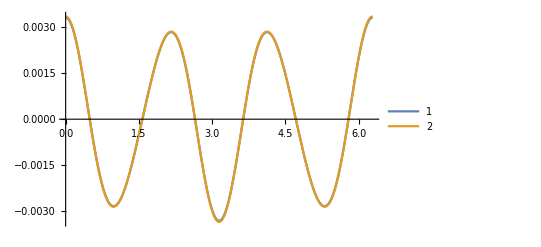

```mathematica
bmu
bJ
Plot[{Sum[dA0s[4,j,theta1],{j,0,5}],dAxs0[4,theta1,bJ]},{theta1,0,2Pi},PlotLegends->Automatic]
```

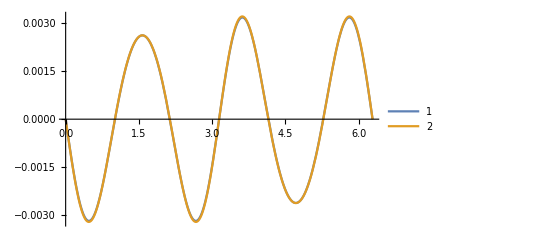

```mathematica
Plot[{Sum[dA0c[4,j,theta1],{j,0,5}],dAxc0[4,theta1,bJ]},{theta1,0,2Pi},PlotLegends->Automatic]
```

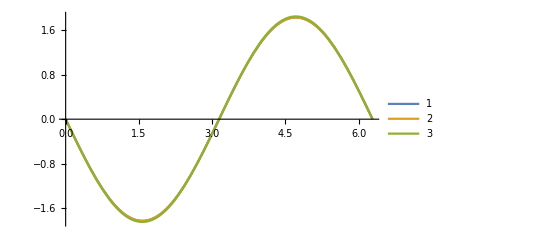

```mathematica
Plot[{Sum[dA0c[0,j,theta1],{j,0,5}],dAxc0[0,theta1,bJ],dAxc0[0,theta1,bJ]*1.01},{theta1,0,2Pi},PlotLegends->Automatic]
```

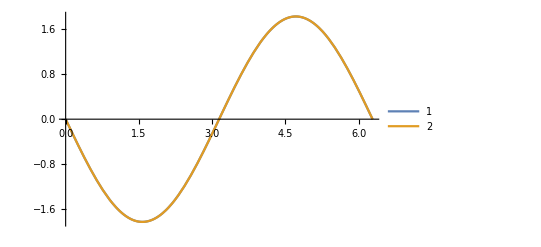

```mathematica
Plot[{Sum[dA0c[0,j,theta1],{j,0,5}],dAxc0[0,theta1,bJ]},{theta1,0,2Pi},PlotLegends->Automatic]
```

```mathematica
dAxc0[3,theta1,bJ]
```

1/325 (-50 BesselI[2,1] Sin[2 theta1]+2 BesselI[3,1] (-Cos[3 theta1] Sin[theta1]-51 Cos[theta1] Sin[3 theta1])-52 BesselI[4,1] Sin[4 theta1])

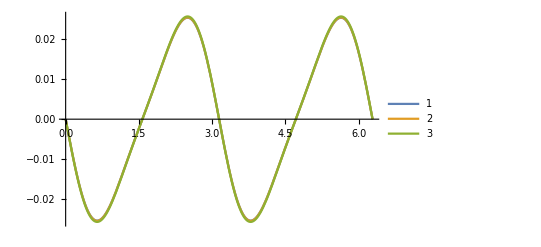

```mathematica
Plot[{Sum[dA0c[3,j,theta1],{j,0,5}],dAxc0[3,theta1,bJ],dAxc0[3,theta1,bJ]*1.01},{theta1,0,2Pi},PlotLegends->Automatic]
```

#### plot for pvns

```mathematica
testpvx10[xi_,xj_]:=Sum[Release[dAxs0[n,theta1,bJ]Sin[n theta2]+dAxc0[n,theta1,bJ]Cos[n theta2]]/.{Qx0->0,bJ->1,bmu->1,theta1->xi,theta2->xj},{n,0,2}]
testpv10[xi_,xj_]:=Sum[dA0s[n,j,xi]Sin[n xj]+dA0c[n,j,xi]Cos[n xj]/.{Qx0->0,bJ->1,bmu->1},{n,0,2},{j,0,5}]
```

```mathematica
nmax=2;
(*pvx10[1,1,xi,xj,nmax];//Simplify
pvx10[1,1,xj,xi,nmax];//Simplify
pv10[1,1,xi,xj];//Simplify
pv10[1,1,xj,xi];//Simplify*)
```

```mathematica
pv10[1,1,theta2,myt2]
```

-(703 Sin[theta2])/384-Cosh[theta2] (-(1-Cosh[2 π]) Csch[2 π]+(1-Cosh[2 π]) Csch[2 π] (1/2 (1-Cosh[2 π])-Sinh[2 π]^2/(2 (1-Cosh[2 π]))))-Cosh[theta2] (-1/10 (6-6 Cosh[2 π]) Csch[2 π]+(1-Cosh[2 π]) Csch[2 π] (1/20 (6-6 Cosh[2 π])-(3 Sinh[2 π]^2)/(10 (1-Cosh[2 π]))))-Cosh[theta2] (-1/40 (11-11 Cosh[2 π]) Csch[2 π]+(1-Cosh[2 π]) Csch[2 π] (1/80 (11-11 Cosh[2 π])-(11 Sinh[2 π]^2)/(80 (1-Cosh[2 π]))))-Cosh[theta2] (-1/80 (6-6 Cosh[2 π]) Csch[2 π]+(1-Cosh[2 π]) Csch[2 π] (1/160 (6-6 Cosh[2 π])-(3 Sinh[2 π]^2)/(80 (1-Cosh[2 π]))))-Cosh[theta2] (-1/960 (17-17 Cosh[2 π]) Csch[2 π]+(1-Cosh[2 π]) Csch[2 π] ((17-17 Cosh[2 π])/1920-(17 Sinh[2 π]^2)/(1920 (1-Cosh[2 π]))))-Cosh[theta2] (-((6-6 Cosh[2 π]) Csch[2 π])/1920+(1-Cosh[2 π]) Csch[2 π] ((6-6 Cosh[2 π])/3840-Sinh[2 π]^2/(640 (1-Cosh[2 π]))))+2 Cosh[2 theta2] (-1/10 (1-Cosh[4 π]) Csch[4 π]+(1-Cosh[4 π]) Csch[4 π] (1/20 (1-Cosh[4 π])-Sinh[4 π]^2/(20 (1-Cosh[4 π]))))+2 Cosh[2 theta2] (-((72-72 Cosh[4 π]) Csch[4 π])/2080+(1-Cosh[4 π]) Csch[4 π] ((72-72 Cosh[4 π])/4160-(9 Sinh[4 π]^2)/(520 (1-Cosh[4 π]))))+2 Cosh[2 theta2] (-((44-44 Cosh[4 π]) Csch[4 π])/3120+(1-Cosh[4 π]) Csch[4 π] ((44-44 Cosh[4 π])/6240-(11 Sinh[4 π]^2)/(1560 (1-Cosh[4 π]))))+2 Cosh[2 theta2] (-((72-72 Cosh[4 π]) Csch[4 π])/24960+(1-Cosh[4 π]) Csch[4 π] ((72-72 Cosh[4 π])/49920-(3 Sinh[4 π]^2)/(2080 (1-Cosh[4 π]))))+2 Cosh[2 theta2] (-((31-31 Cosh[4 π]) Csch[4 π])/49920+(1-Cosh[4 π]) Csch[4 π] ((31-31 Cosh[4 π])/99840-(31 Sinh[4 π]^2)/(99840 (1-Cosh[4 π]))))+Sinh[theta2]-(1/2 (1-Cosh[2 π])-Sinh[2 π]^2/(2 (1-Cosh[2 π]))) Sinh[theta2]-(1/20 (6-6 Cosh[2 π])-(3 Sinh[2 π]^2)/(10 (1-Cosh[2 π]))) Sinh[theta2]-(1/80 (11-11 Cosh[2 π])-(11 Sinh[2 π]^2)/(80 (1-Cosh[2 π]))) Sinh[theta2]-(1/160 (6-6 Cosh[2 π])-(3 Sinh[2 π]^2)/(80 (1-Cosh[2 π]))) Sinh[theta2]-((17-17 Cosh[2 π])/1920-(17 Sinh[2 π]^2)/(1920 (1-Cosh[2 π]))) Sinh[theta2]-((6-6 Cosh[2 π])/3840-Sinh[2 π]^2/(640 (1-Cosh[2 π]))) Sinh[theta2]+217/960 (Sin[2 theta2]+3 Sinh[theta2])+1/40 (2 Sin[2 theta2]+11 Sinh[theta2])+1/960 (4 Sin[2 theta2]+17 Sinh[theta2])+(-39 Sin[theta2]-15 Sin[3 theta2]-88 Sinh[2 theta2])/3120+(-26 Sin[theta2]-15 Sin[3 theta2]-62 Sinh[2 theta2])/49920+1/480 (-13 Sin[theta2]-15 Sin[3 theta2]-36 Sinh[2 theta2])+1/10 (-Sin[theta2]-2 Sinh[2 theta2])+2 (1/20 (1-Cosh[4 π])-Sinh[4 π]^2/(20 (1-Cosh[4 π]))) Sinh[2 theta2]+2 ((72-72 Cosh[4 π])/4160-(9 Sinh[4 π]^2)/(520 (1-Cosh[4 π]))) Sinh[2 theta2]+2 ((44-44 Cosh[4 π])/6240-(11 Sinh[4 π]^2)/(1560 (1-Cosh[4 π]))) Sinh[2 theta2]+2 ((72-72 Cosh[4 π])/49920-(3 Sinh[4 π]^2)/(2080 (1-Cosh[4 π]))) Sinh[2 theta2]+2 ((31-31 Cosh[4 π])/99840-(31 Sinh[4 π]^2)/(99840 (1-Cosh[4 π]))) Sinh[2 theta2]

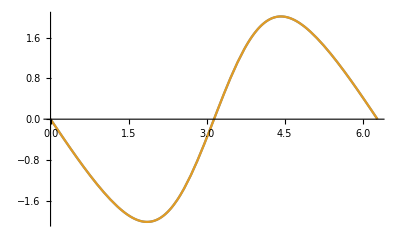

```mathematica
Plot[{(-98384 Sin[theta2]+13988 Sin[2 theta2]-1815 Sin[3 theta2])/49920,pv10[1,1,theta2,myt2]},{theta2,0,2Pi}];
```

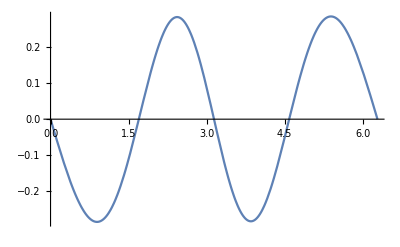

```mathematica
Plot[{testpv10[theta2,myt2]-pv10[1,1,theta2,myt2]},{theta2,0,2Pi}];
```

```mathematica
testpv10[1.0,myt2]
pv10[1,1,1.0,myt2]
```

-1.40874

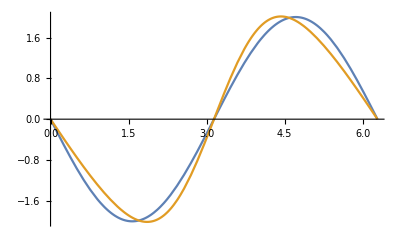

```mathematica
Plot[{Simplify[testpv10[theta2,myt2]],Simplify[pv10[1,1,theta2,myt2]]},{theta2,0,2Pi},PlotStyle->{Blue,Green}]
```

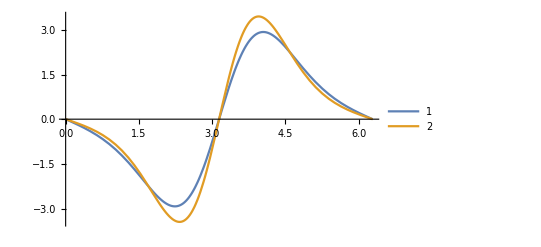

```mathematica
Plot[{testpv10[theta2,myt2]*Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

```mathematica
myt2=Pi;
Plot[{testpv10[theta2,myt2]*Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pvx10[1,1,theta2,myt2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

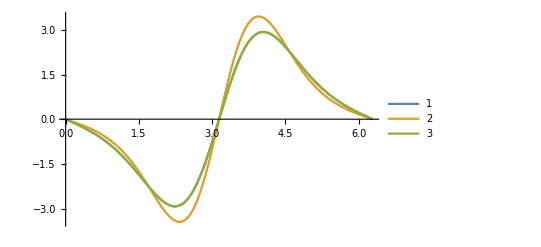

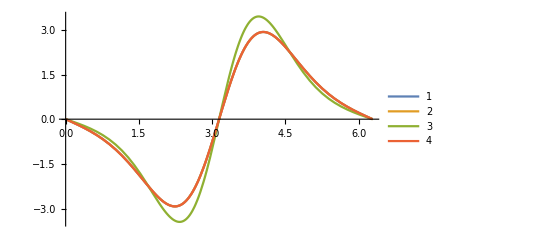

-(BesselI[0,1]+BesselI[1,1]) Sin[xi]+1/5 Cos[xj] (-4 BesselI[1,1] Cos[xi] Sin[xi]-2 BesselI[2,1] Sin[2 xi])+1/65 Cos[2 xj] (-13 BesselI[1,1] Sin[xi]+2 BesselI[2,1] (-Cos[2 xi] Sin[xi]-14 Cos[xi] Sin[2 xi])-15 BesselI[3,1] Sin[3 xi])+1/5 (-2 (-BesselI[0,1]+BesselI[1,1]) Cos[xi]^2-2 (BesselI[0,1]-BesselI[1,1]) Sin[xi]^2) Sin[xj]+1/65 (-4 (BesselI[2,1]+7 (-BesselI[1,1]+BesselI[2,1])) Cos[xi] Cos[2 xi]-2 (BesselI[1,1]-29 BesselI[2,1]) Sin[xi] Sin[2 xi]) Sin[2 xj]

-(BesselI[0,1]+BesselI[1,1]) Sin[xj]+1/5 Sin[xi] (-2 (-BesselI[0,1]+BesselI[1,1]) Cos[xj]^2-2 (BesselI[0,1]-BesselI[1,1]) Sin[xj]^2)+1/5 Cos[xi] (-4 BesselI[1,1] Cos[xj] Sin[xj]-2 BesselI[2,1] Sin[2 xj])+1/65 Sin[2 xi] (-4 (BesselI[2,1]+7 (-BesselI[1,1]+BesselI[2,1])) Cos[xj] Cos[2 xj]-2 (BesselI[1,1]-29 BesselI[2,1]) Sin[xj] Sin[2 xj])+1/65 Cos[2 xi] (-13 BesselI[1,1] Sin[xj]+2 BesselI[2,1] (-Cos[2 xj] Sin[xj]-14 Cos[xj] Sin[2 xj])-15 BesselI[3,1] Sin[3 xj])

```mathematica
myt2=Pi;
Plot[{testpvx10[theta2,myt2]*Exp[Cos[theta2-myt2]],testpv10[theta2,myt2]*Exp[Cos[theta2-myt2]],pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pvx10[1,1,theta2,myt2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

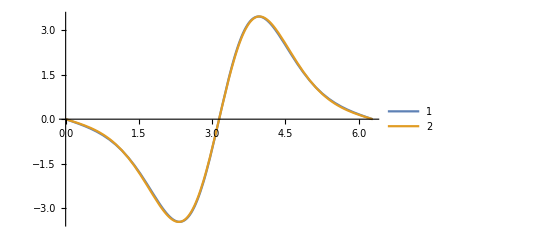

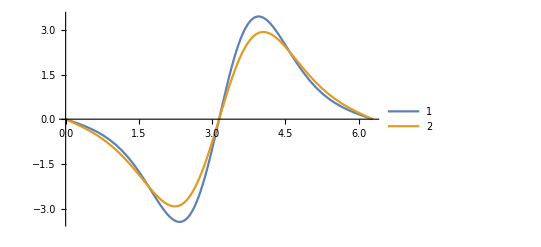

```mathematica
nmax=2;jmax=5;
myt2=myt2;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pvx10[1,1,theta2,myt2,nmax]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

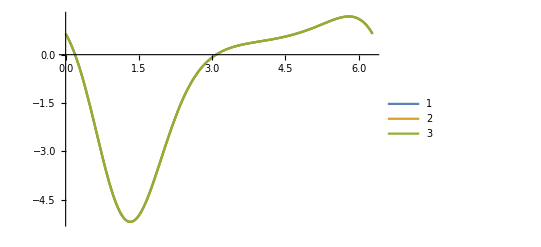

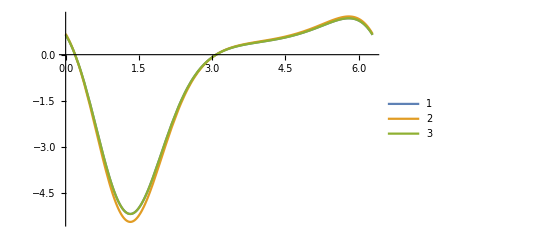

```mathematica
nmax=4;jmax=5;
myt2=Pi/3;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]],pvx20[1,1,myt2,theta2,4]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]]*1.05,pvx20[1,1,myt2,theta2,4]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

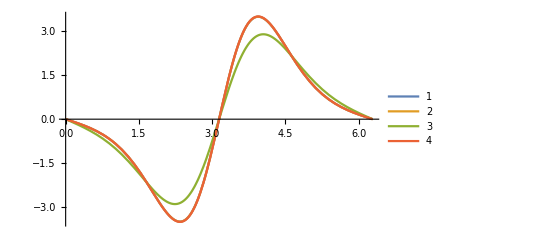

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]],pv20[1,1,myt2,theta2]Exp[Cos[theta2-myt2]],pvx10[1,1,theta2,myt2,4]Exp[Cos[theta2-myt2]],pvx20[1,1,myt2,theta2,4]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotLegends->Automatic]
```

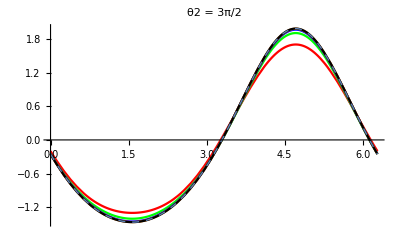

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,theta2],{theta2,0,2Pi},PlotStyle->{Dashed,Thick}];
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```